### Categorization

Tutorial

Toolbox

Toolbox`

Toolbox/tutorial/Constraint-based modeling

### Keywords

Details

# Constraint-based modeling

The following sections provide a very general introduction into the constraint-based modeling capabilities of the toolbox. More detailed information can be obtained from the individual documentation pages of the respective commands. A primer and a review of constraint-based modeling can be found here or here.

Load the package

```mathematica
Needs["Toolbox`"]
```

Load a model of Escherichia coli central metabolism

```mathematica
ecoli=ExampleData[{"Toolbox","EcoliCore"}];
```

### Constraints

Constraint-based modeling evaluates phenotypes in the light of biological, physical, and chemical constraints. One important type of constraints are flux capacities, e.g, a reaction is irrversible under physiological conditions and can thus carry only positive net-flux. Toolbox models provide a Constraints attribute where this kind of information can be included. Lower and upper bounds on reactions fluxes are encoded using rules of flux identifiers and pairs of

v_id→{lowerBound, upperBound} | Single flux constraint
getConstraints[model] or model["Constraints"] | access the model constraints
setConstraints[model, constr] | overwrite previous constraints with new constraints (constr)
updateConstraints[model, constr] | udpate existing constraints with new constraints (constr)

Dealing with constraints

Query all available constraints.

```mathematica
ecoli["Constraints"]
```

{v_AKGDH→{0,∞},v_ATPM→{0,∞},v_(Biomass_Ecoli_core_N(w/GAM)_Nmet2)→{0,∞},v_CS→{0,∞},v_CYTBD→{0,∞},v_FBP→{0,∞},v_FORt2→{0,∞},v_FORti→{0,∞},v_FRD7→{0,∞},v_FRUpts2→{0,∞},v_FUMt2_2→{0,∞},v_GLCpts→{0,∞},v_GLNS→{0,∞},v_GLNabc→{0,∞},v_GLUN→{0,∞},v_GLUSy→{0,∞},v_GND→{0,∞},v_ICL→{0,∞},v_MALS→{0,∞},v_MALt2_2→{0,∞},v_ME1→{0,∞},v_ME2→{0,∞},v_NADH16→{0,∞},v_NADTRHD→{0,∞},v_PDH→{0,∞},v_PFK→{0,∞},v_PFL→{0,∞},v_PGL→{0,∞},v_PPC→{0,∞},v_PPCK→{0,∞},v_PPS→{0,∞},v_PYK→{0,∞},v_SUCCt2_2→{0,∞},v_SUCCt3→{0,∞},v_SUCDi→{0,∞},v_THD2→{0,∞},v_(EX_ac(e))→{-∞,0},v_(EX_acald(e))→{-∞,0},v_(EX_akg(e))→{-∞,0},v_(EX_co2(e))→{-∞,0},v_(EX_etoh(e))→{-∞,0},v_(EX_for(e))→{-∞,0},v_(EX_fru(e))→{-∞,0},v_(EX_fum(e))→{-∞,0},v_(EX_glc(e))→{-∞,0},v_(EX_gln_L(e))→{-∞,0},v_(EX_glu_L(e))→{-∞,0},v_(EX_h2o(e))→{-∞,0},v_(EX_h(e))→{-∞,0},v_(EX_lac_D(e))→{-∞,0},v_(EX_mal_L(e))→{-∞,0},v_(EX_nh4(e))→{-∞,0},v_(EX_o2(e))→{-∞,0},v_(EX_pi(e))→{-∞,0},v_(EX_pyr(e))→{-∞,0},v_(EX_succ(e))→{-∞,0},v_GLYK→{0,∞},v_(EX_glyc(e))→{-∞,0}}

Looking at the flux bounds of all availabe exchange reactions reveals that the current model can only infinitely secrete but not take up any matter.

```mathematica
SlideView[#->(v[getID[#]]/.ecoli["Constraints"])&/@getExchanges[ecoli]]
```

Change a few exchange reaction flux bounds to reflect an aerobic minimal glucose medium.

```mathematica
updateConstraints[ecoli,{Subscript[v, EX_glc(e)]->{-∞,10},Subscript[v, EX_o2(e)]->{-∞,∞},Subscript[v, EX_pi(e)]->{-∞,∞},Subscript[v, EX_h(e)]->{-∞,∞},Subscript[v, EX_nh4(e)]->{-∞,∞}}];
```

### Flux-balance and flux-variability analysis

Flux-balance analysis (FBA) finds a steady-state flux solution that maxmizes a cellular objective, e.g., optimal growth rate. For example, FBA can be used to asses the consequence of genetic perturbations. Flux-variablity analysis (FVA) calculates effective flux bounds by minimizing and maximizing flux through individual reactions. For example, FBA solutions are rarely unique and FVA can be used to assess the space of alternativa optimal solutions.

fba[model, obj] | find a steady-state flux distribution that maximizes obj
fva[model] | find minimum and maximum fluxes for all reactions in model
XXXX | XXXX

Basic COBRA functionality

Perform FBA.

```mathematica
obj=Subscript[v, Biomass_Ecoli_core_N(w/GAM)_Nmet2];
fluxes=fba[ecoli,obj]//Chop
```

{v_ACALD→0,v_ACALDt→0,v_ACKr→0,v_ACONTa→5.12759,v_ACONTb→5.12759,v_ACt2r→0,v_ADK1→0,v_AKGDH→4.13861,v_AKGt2r→0,v_ALCD2x→0,v_ATPM→0,v_ATPS4r→41.2857,v_(Biomass_Ecoli_core_N(w/GAM)_Nmet2)→0.916647,v_CO2t→-20.9916,v_CS→5.12759,v_CYTBD→39.8637,v_D_LACt2→0,v_ENO→14.2623,v_ETOHt2r→0,v_FBA→7.15849,v_FBP→0,v_FORt2→0,v_FORti→0,v_FRD7→0,v_FRUpts2→0,v_FUM→4.13861,v_FUMt2_2→0,v_G6PDH2r→5.78916,v_GAPD→15.6336,v_GLCpts→10.,v_GLNS→0.234387,v_GLNabc→0,v_GLUDy→-4.76391,v_GLUN→0,v_GLUSy→0,v_GLUt2r→0,v_GND→5.78916,v_H2Ot→-27.6688,v_ICDHyr→5.12759,v_ICL→0,v_LDH_D→0,v_MALS→0,v_MALt2_2→0,v_MDH→4.13861,v_ME1→0,v_ME2→0,v_NADH16→35.7251,v_NADTRHD→0,v_NH4t→4.9983,v_O2t→19.9319,v_PDH→8.563,v_PFK→7.15849,v_PFL→0,v_PGI→4.02293,v_PGK→-15.6336,v_PGL→5.78916,v_PGM→-14.2623,v_PIt2r→3.37207,v_PPC→2.62674,v_PPCK→0,v_PPS→0,v_PTAr→0,v_PYK→1.15968,v_PYRt2r→0,v_RPE→3.20055,v_RPI→-2.58861,v_SUCCt2_2→0,v_SUCCt3→0,v_SUCDi→4.13861,v_SUCOAS→-4.13861,v_TALA→1.76573,v_THD2→0,v_TKT1→1.76573,v_TKT2→1.43482,v_TPI→7.15849,v_(EX_ac(e))→0,v_(EX_acald(e))→0,v_(EX_akg(e))→0,v_(EX_co2(e))→-20.9916,v_(EX_etoh(e))→0,v_(EX_for(e))→0,v_(EX_fru(e))→0,v_(EX_fum(e))→0,v_(EX_glc(e))→10.,v_(EX_gln_L(e))→0,v_(EX_glu_L(e))→0,v_(EX_h2o(e))→-27.6688,v_(EX_h(e))→-18.3879,v_(EX_lac_D(e))→0,v_(EX_mal_L(e))→0,v_(EX_nh4(e))→4.9983,v_(EX_o2(e))→19.9319,v_(EX_pi(e))→3.37207,v_(EX_pyr(e))→0,v_(EX_succ(e))→0,v_GLYK→0,v_G3PD2→0,v_(EX_glyc(e))→0}

Visualize the fluxes on a pathway map.

```mathematica
{cmpd,rxns,text}=ExampleData[{"Toolbox","EcoliCoreMap"}];
drawPathway[cmpd,rxns,Flatten@text,ReactionData->Select[fluxes,#[[2]]≠0&],PlotLegends->{LegendLabel->"Flux\nmmol h^-1 gDW^-1"}]
```

-Graphics-

Perform FVA.

```mathematica
fvaSol=fva[ecoli]//Chop
```

{v_ACALD→{-20.,0},v_ACALDt→{-20.,0},v_ACKr→{-20.,0},v_ACONTa→{0,20.},v_ACONTb→{0,20.},v_ACt2r→{-20.,0},v_ADK1→{0,175.},v_AKGDH→{0,20.},v_AKGt2r→{-10.,0},v_ALCD2x→{-20.,0},v_ATPM→{0,175.},v_ATPS4r→{-40.,150.},v_(Biomass_Ecoli_core_N(w/GAM)_Nmet2)→{0,0.916647},v_CO2t→{-60.,0},v_CS→{0,20.},v_CYTBD→{0,120.},v_D_LACt2→{-20.,0},v_ENO→{0,20.},v_ETOHt2r→{-20.,0},v_FBA→{-10.,10.},v_FBP→{0,175.},v_FORt2→{0,700.},v_FORti→{0,700.},v_FRD7→{0,∞},v_FRUpts2→{0,0},v_FUM→{-15.,20.},v_FUMt2_2→{0,0},v_G6PDH2r→{0,60.},v_GAPD→{0,20.},v_GLCpts→{0,10.},v_GLNS→{0,175.},v_GLNabc→{0,0},v_GLUDy→{-10.,175.},v_GLUN→{0,175.},v_GLUSy→{0,175.},v_GLUt2r→{-10.,0},v_GND→{0,60.},v_H2Ot→{-60.,0},v_ICDHyr→{0,20.},v_ICL→{0,20.},v_LDH_D→{-20.,0},v_MALS→{0,20.},v_MALt2_2→{0,0},v_MDH→{-72.5,40.},v_ME1→{0,102.5},v_ME2→{0,102.5},v_NADH16→{0,120.},v_NADTRHD→{0,395.},v_NH4t→{0,10.},v_O2t→{0,60.},v_PDH→{0,40.},v_PFK→{0,185.},v_PFL→{0,40.},v_PGI→{-50.,10.},v_PGK→{-20.,0},v_PGL→{0,60.},v_PGM→{-20.,0},v_PIt2r→{0,3.37207},v_PPC→{0,175.},v_PPCK→{0,175.},v_PPS→{0,175.},v_PTAr→{0,20.},v_PYK→{0,185.},v_PYRt2r→{-20.,0},v_RPE→{-0.650406,40.},v_RPI→{-20.,0},v_SUCCt2_2→{0,233.333},v_SUCCt3→{0,233.333},v_SUCDi→{0,∞},v_SUCOAS→{-20.,0},v_TALA→{-0.161878,20.},v_THD2→{0,350.},v_TKT1→{-0.161878,20.},v_TKT2→{-0.488528,20.},v_TPI→{-10.,10.},v_(EX_ac(e))→{-20.,0},v_(EX_acald(e))→{-20.,0},v_(EX_akg(e))→{-10.,0},v_(EX_co2(e))→{-60.,0},v_(EX_etoh(e))→{-20.,0},v_(EX_for(e))→{-40.,0},v_(EX_fru(e))→{0,0},v_(EX_fum(e))→{0,0},v_(EX_glc(e))→{0,10.},v_(EX_gln_L(e))→{0,0},v_(EX_glu_L(e))→{-10.,0},v_(EX_h2o(e))→{-60.,0},v_(EX_h(e))→{-40.,0},v_(EX_lac_D(e))→{-20.,0},v_(EX_mal_L(e))→{0,0},v_(EX_nh4(e))→{0,10.},v_(EX_o2(e))→{0,60.},v_(EX_pi(e))→{0,3.37207},v_(EX_pyr(e))→{-20.,0},v_(EX_succ(e))→{-15.,0},v_GLYK→{0,0},v_G3PD2→{0,0},v_(EX_glyc(e))→{0,0}}

Visualize FVA result.

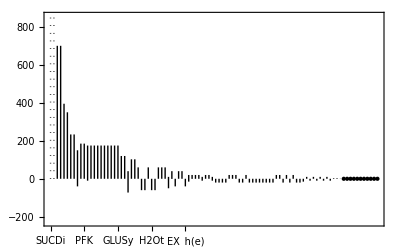

```mathematica
plotFVA[fvaSol]
```

### High-throughput data integration

In progress ...

gimme[...] | find a steady-state flux distribution that maximizes obj and matches data
XXXX | XXXX
XXXX | XXXX

XXXX.

Perform GIMME

```mathematica
gimme[ecoli, data]
```

### Changing linear programming solver back-ends

Per default, the toolbox uses Mathematica's built-in linerar programming solver (LinerarProgramming). Depending on the availability of other optimization tools, different solver back-ends can be used to solve constraint-based modeling problems.

LinearProgramming | Mathematica's internal linear programming solver
GurobiSolve | MathLink interface to Gurobi
GLPKStandalone | Interface to the GLPK standalone solver
CPLEXStandalone | Interface to the CPLEX standalone solver

Supported solver back-ends

Use GLPKStandalone instead of LinearProgramming

```mathematica
fba[ecoli,obj,Solver->CPLEXStandalone]//Short
```

{v_ACALD→0,v_ACALDt→0,v_ACKr→0,v_ACONTa→5.12759,«90»,v_(EX_succ(e))→0,v_GLYK→0,v_G3PD2→0,v_(EX_glyc(e))→0}

More About

Related Tutorials

Related Wolfram Education Group Courses